# Derivative Graphs

## Given f (x) graph, find/create f' graph

Consider the graph of f(x) shown below.

Use the slider and notice how the slope changes. Make a special note where the slope (derivative) is zero, positive, or negative:

```mathematica
f[x_]:=(1/3)x^3-x^2-3x+6;
Manipulate[Plot[{f[a]+f'[a]*(x-a),f[x]},{x,-3,5},PlotRange->{-5,8},PlotStyle->{Red,Blue},Epilog->{Red,PointSize[.015],Point@{a,f[a]}}
],{a,-2.2,4.5},SaveDefinitions->True]
```

Below is the graph of f' along with the graph of f.

Complete the following statements:

When the tangent line to f(x) is “flat,” then the graph of f' ...
When the graph of f(x) increasing, then the graph of f' ...
When the graph of f(x) decreasing, then the graph of f' ...

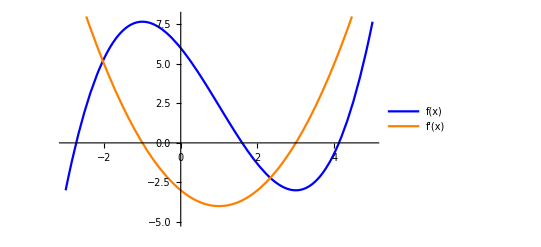

```mathematica
Plot[{f[x],f'[x]},{x,-3,5},PlotRange->{-5,8},PlotLegends->"Expressions",PlotStyle->{Blue,Orange}]
```

## Finding the f''(x) graph

To find the graph of f''(x), a similar process can be used. In the same way we completed a “slope analysis” of f(x) to find the graph of f'(x), we can do a “slope analysis” of f'(x) to find the graph of f''(x).

Use the orange f'(x) graph above to answer the following questions:

Where does f''(x)=0 (the slope of f'(x)=0)?

Over what intervals is f''(x) (the slope of f'(x) ) positive and negative?

f''(x)>0 over...
f''(x)<0 over...

Run the following input cell to check your answer:

```mathematica
f[x_]:=(1/3)x^3-x^2-3x+6;
Plot[{f[x],f'[x],f''[x]},{x,-3,5},PlotRange->{-5,8},PlotLegends->"Expressions",PlotStyle->{Blue,Orange,Green}]
```

A common test or quiz question would give you the graph of f and you would need to sketch the graph of f' or f'' , or select the correct one from a list of choices.

## Going Backward

You can do this analysis in reverse to create the graph of f if you are given the graph of f'.

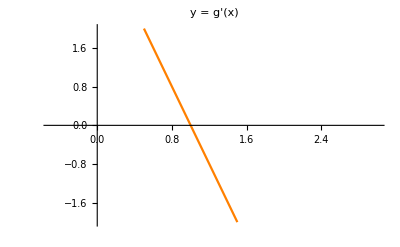

```mathematica
g[x_]:=-2(x-1)^2+1;
Plot[g'[x],{x,-.5,3},PlotRange->{-2,2},PlotStyle->{Orange},PlotLabel->"y = g'(x)"]
```

Look at the orange y=g'(x) above and answer the following:

Since g'(x)=0 at x=1, then the graph of g(x) will look like what at x=1?

Since g'(x) is positive for x<1, then the graph of g(x) will do what for x<1?

Since g'(x) is negative for x>1, then the graph of g(x) will do what at x>1?

Run the following input cell to check your answer:

```mathematica
g[x_]:=-2(x-1)^2+1;
Plot[{g'[x],g[x],g[x]+.5,g[x]-1.2},{x,-.5,3},PlotRange->{-2,2},PlotStyle->{Orange,Blue,Green,Magenta}]
```

The Green, Blue, and Magenta graphs are all possible answers for g(x). 
It may seem surprising that there are many solutions...all share the same shape but are vertical shifts of each other.

Challenge question: Why is this true?

## Practice

Each graph below shows a function, the first derivative, and the second derivative:

Type the color of each graph on the axis below:

f :
f' : 
f'' :

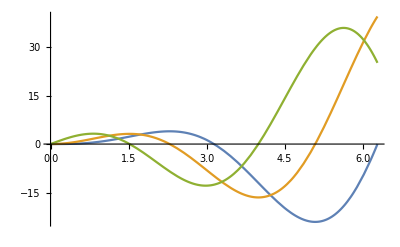

```mathematica
Clear[f,g]
f[x_]:=x^2 Sin[x]
Plot[{f[x],f'[x],f''[x]},{x,0,2 π}]
```

Type the color of each graph on the axis below:

g :
g' : 
g'' :

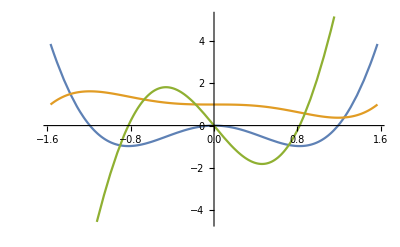

```mathematica
g[x_]:=-x^3 Cos[x]+1
Plot[{g'[x],g[x],g''[x]},{x,-π/2,π/2}]
```

Run the following input cell to check your answer:

```mathematica
Clear[f,g]
f[x_]:=x^2 Sin[x]
Plot[{f[x],f'[x],f''[x]},{x,0,2 π},PlotLegends->"Expressions"]
g[x_]:=-x^3 Cos[x]+1
Plot[{g'[x],g[x],g''[x]},{x,-π/2,π/2},PlotLegends->"Expressions"]
```

## f'' and Concavity of f(x)

The graph of f(x) is concave up if a tangent line is below the graph of f, like y=x^2.
The graph of f(x) is concave down if a tangent line is above the graph of f, like y=-x^2.

```mathematica
GraphicsGrid[{{Plot[x^2,{x,-3,3},PlotRange->{-3,3}],Plot[-x^2,{x,-3,3},PlotRange->{-3,3}]}}]
```

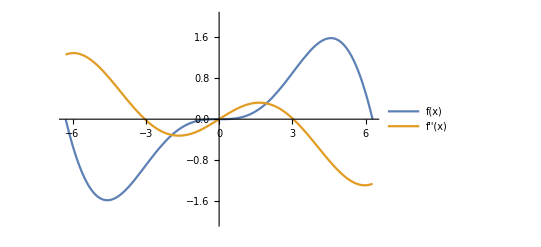

```mathematica
f[x_]:=x^2 Sin[x/2]/10;
Plot[{f[x],f''[x]},{x,-2π,2π},PlotRange->{-2,2},PlotLegends->"Expressions"]
```

#### Connections:

When the graph of f(x) is concave UP, f''>0 and the graph of f'' is above the x-axis.

When the graph of f(x) is concave DOWN, f''<0 and the graph of f'' is below the x-axis.

## Authorship Information

Dan Uhlman
uhlmand@tas.tw